Estimate parameters for stock return rate

z_(t+1)=μ+ϕ z_t+σ ϵ_t

```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
SeedRandom[0];
```

```mathematica
csv = Import["./000006.csv","CSV"];
```

```mathematica
csv//Dimensions
```

{613,15}

```mathematica
x=N[10^-9+csv[[2;;,4]]];
```

```mathematica
y1=Drop[x,1];
y=Drop[x,-1];
z=(y1-y)/y;
ζ1=Drop[z,1];
ζ=Drop[z,-1];
```

```mathematica
UP[ϕ_,μ_,σ_]:=(ϕ-1)^2/2+μ^2/2+σ^2/2;
```

```mathematica
f[ϕ_,μ_,σ_]:=Sum[1/2((ζ1[[i]]- μ-ϕ ζ[[i]])/σ)^2+Log[√(2 π) ]+1/2 Log[σ^2],{i,1,Length[ζ]}];
```

```mathematica
HessianH[f_,x_List?VectorQ]:=D[f,{x,2}]
```

```mathematica
GradientG[f_,x_List?VectorQ]:=D[f,{x,1}]
```

```mathematica
U[ϕ_ ,μ_,σ_]=N[Simplify[f[ϕ,μ,σ]+UP[ϕ,μ,σ]]];
```

```mathematica
dU[ϕ_,μ_,σ_]=Simplify[GradientG[U[ϕ,μ,σ],{ϕ,μ,σ}]];
```

```mathematica
ddU[ϕ_,μ_,σ_]=Simplify[HessianH[U[ϕ,μ,σ],{ϕ,μ,σ}]];
```

```mathematica
QS=hmc[U,dU,ddU,3,5000,10000,True,True];
```

1001 71.8793 13.4169 0.271731 0.39288 -13760.8 -13688.9 -12764.2 0.000117391 0.0221938 True {1,3,11} {2,7,8,10,11}

2002 562.797 0.011534 0.416503 0.473381 -13759.6 -13710.7 -13196.8 0.000117391 0.032494 False {1,2,8,11} {1,8,10,11}

3003 41.5659 16.8369 0.532524 0.434303 -13756.7 -13715.1 -13470.9 0.000117391 0.0432495 True {2,3,4,5,7,10,11} {1,11}

4004 132.071 0.0108247 0.449297 0.450596 -13758. -13719.4 -13626. 0.000117391 0.0696537 False {1,2,3,5,11} {1,11}

5005 41.4937 15.8892 0.305136 0.360982 -13760.9 -13719.4 -13685. 0.000117391 0.0927091 True {1,3} {6,8,9,10,11}

6006 78.7926 0.00719935 0.292826 0.424341 -13763.7 -13719.4 -13685. 0.000117391 0.0927091 False {1,2,11} {1,6,11}

7007 42.4328 15.096 0.12226 0.119295 -13761.9 -13719.4 -13685. 0.000117391 0.0927091 True {1,2,3,4} {9,11}

8008 70.8219 0.0096636 0.42409 0.500296 -13755.8 -13719.4 -13685. 0.000117391 0.0927091 False {1,4,6,8,9,11} {1,5,11}

9009 40.7726 14.0863 0.424475 0.387057 -13760.2 -13719.4 -13685. 0.000117391 0.0927091 True {1,3,5} {8,9,10,11}

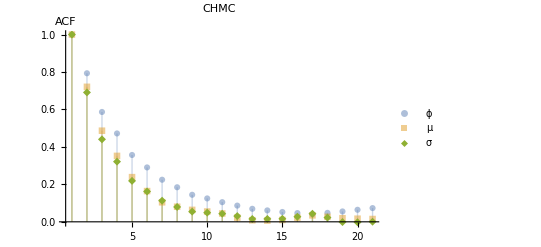

```mathematica
QS1=Table[QS[[i]],{i,1,50000,10}];
ListPlot[{CorrelationFunction[QS1[[;;,1]],{20}],CorrelationFunction[QS1[[;;,2]],{20}],CorrelationFunction[QS1[[;;,3]],{20}]},Filling->Axis,PlotRange->All,AxesLabel->{None,"ACF"},PlotLabel->CHMC,PlotLegends->{ϕ,μ,σ},PlotMarkers->Automatic,PlotStyle->{Opacity[.5],Opacity[.5],Opacity[1]}]
```

```mathematica
ϕ1=QS[[All,1]];
μ1=QS[[All,2]];
σ1=Abs[QS[[All,3]]];
{StandardDeviation[ϕ1],Mean[ϕ1]}
{StandardDeviation[μ1],Mean[μ1]}
{StandardDeviation[σ1],Mean[σ1]}
```

{0.0434732,0.0911853}

{0.000625684,0.000459118}

{0.000445088,0.0253294}

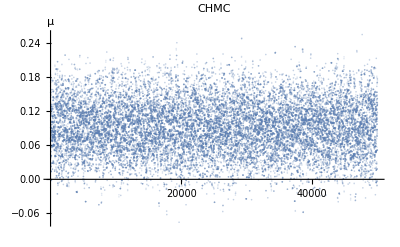

```mathematica
ListPlot[QS[[All,1]],PlotStyle->Opacity[.2],PlotLabel->"CHMC",Ticks->{{20000,40000},Automatic},AxesLabel->{None,"μ"}]
```

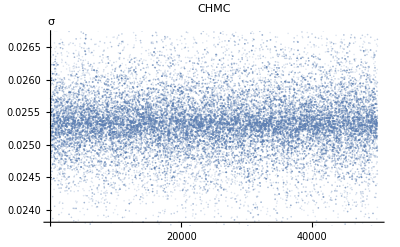

```mathematica
ListPlot[Abs[QS[[All,3]]],PlotStyle->Opacity[.2],PlotLabel->"CHMC",Ticks->{{20000,40000},Automatic},AxesLabel->{None,"σ"}]
```

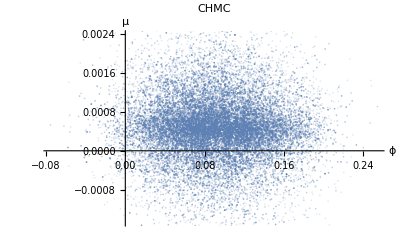

```mathematica
ListPlot[QS[[All,1;;2]],AxesLabel->{ϕ,μ},PlotLabel->"CHMC",PlotStyle->Opacity[0.2]]
```

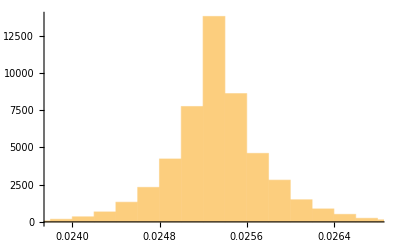

```mathematica
Histogram[Abs[QS[[All,3]]]]
```

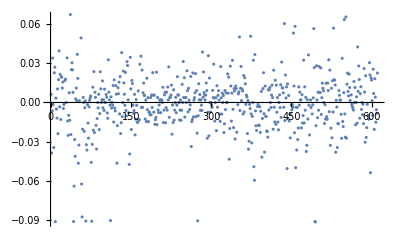

```mathematica
ListPlot[z]
```